```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/m0/m0_500/check

```mathematica
dataall=Import["./Shi_mu=640_m0=500.0-flag_4-21x120_VC=true.csv"];
```

```mathematica
n=Length[Table[i,{i,0,800,10}]]
```

81

```mathematica
dataall[[1]]
```

```mathematica
pdata=Table[Table[dataall[[j*120+i]][[5]],{i,2,121}],{j,0,20}];
```

```mathematica
Dimensions[pdata]
```

{21,120}

```mathematica
Table[Export["./mub"<>ToString[640]<>"/V"<>ToString[j]<>".dat",pdata[[j]]],{j,1,21}];
```

```mathematica
T=Table[i,{i,1,120}];
```

```mathematica
Length[pdata[[1]]]
```

21

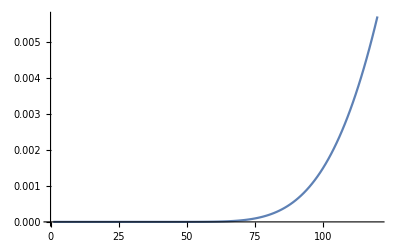

```mathematica
ListLinePlot[pdata[[1]][[10]]*197.33^3/T^4,PlotRange->All]
```